### PARAMETRES

```mathematica
listH ={100,10,100} (*мощности слоев*)
alpha = 10 Degree (*наклон слоев*)
len = 100(*длина профиля*)
dx = 3(*шаг по профилю*)
anoMaxDisp = 100(*степень складчатости нижнего слоя в метрах*)
hTapering =5  (*степень влияния нижнего горизонта на верхние*)
listV = {1000,2000,3000, 4000} (*набор скоростей*)
numOfWells = 10 (*кол скважин*)
wellsLocation = "min" (*расположение скважин "max","min","regular","random"*)
```

{100,10,100}

10 °

100

3

100

5

{1000,2000,3000,4000}

10

min

### DEPTH

```mathematica
horNHsorted = BuildDepthSection[listH,alpha,len,dx,anoMaxDisp,hTapering][["horNHsorted"]]
```

{{{0,6},{3,11},{6,16},{9,20},{12,25},{15,29},{18,31},{21,34},{24,35},{27,36},{30,35},{33,35},{36,34},{39,32},{42,30},{45,28},{48,27},{51,25},{54,24},{57,23},{60,22},{63,22},{66,23},{69,25},{72,27},{75,30},{78,34},{81,39},{84,42},{87,47},{90,54},{93,58},{96,63},{99,67}},{{0,-98},{3,-91},{6,-87},{9,-81},{12,-77},{15,-72},{18,-69},{21,-67},{24,-66},{27,-65},{30,-65},{33,-67},{36,-68},{39,-70},{42,-73},{45,-75},{48,-78},{51,-80},{54,-82},{57,-83},{60,-84},{63,-84},{66,-83},{69,-82},{72,-79},{75,-75},{78,-71},{81,-67},{84,-62},{87,-55},{90,-50},{93,-45},{96,-40},{99,-34}},{{0,-129},{3,-118},{6,-109},{9,-101},{12,-93},{15,-86},{18,-80},{21,-77},{24,-76},{27,-76},{30,-77},{33,-80},{36,-85},{39,-91},{42,-97},{45,-104},{48,-111},{51,-116},{54,-120},{57,-126},{60,-129},{63,-129},{66,-130},{69,-127},{72,-121},{75,-116},{78,-109},{81,-101},{84,-91},{87,-82},{90,-73},{93,-66},{96,-58},{99,-51}},{{0,-266},{3,-250},{6,-231},{9,-211},{12,-197},{15,-188},{18,-180},{21,-177},{24,-181},{27,-185},{30,-189},{33,-196},{36,-205},{39,-214},{42,-222},{45,-226},{48,-232},{51,-244},{54,-251},{57,-255},{60,-263},{63,-272},{66,-276},{69,-272},{72,-270},{75,-260},{78,-248},{81,-232},{84,-214},{87,-199},{90,-183},{93,-169},{96,-159},{99,-157}}}

```mathematica
PlotDepthSection[horNHsorted]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horNHsorted,listV][["velModel"]]
datasetVelModel=BuildVelocitySection[horNHsorted,listV][["datasetVelModel"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horNHsorted]
```

-Graphics-

### TIME

```mathematica
timeNH=BuildTimeSection[horNHsorted, velModel][["timeNH"]]
```

{{{0,0},{3,0},{6,0},{9,0},{12,0},{15,0},{18,0},{21,0},{24,0},{27,0},{30,0},{33,0},{36,0},{39,0},{42,0},{45,0},{48,0},{51,0},{54,0},{57,0},{60,0},{63,0},{66,0},{69,0},{72,0},{75,0},{78,0},{81,0},{84,0},{87,0},{90,0},{93,0},{96,0},{99,0}},{{0,0.0899322},{3,0.0908532},{6,0.0944841},{9,0.0946092},{12,0.0980073},{15,0.0989398},{18,0.0995458},{21,0.101554},{24,0.101846},{27,0.101854},{30,0.100473},{33,0.101842},{36,0.100596},{39,0.09913},{42,0.0986882},{45,0.0971214},{48,0.0976746},{51,0.0964942},{54,0.0966047},{57,0.0955008},{60,0.0948494},{63,0.0948494},{66,0.0949444},{69,0.0967178},{72,0.097101},{75,0.0975711},{78,0.0994182},{81,0.102477},{84,0.102703},{87,0.103194},{90,0.107546},{93,0.108374},{96,0.110351},{99,0.110284}},{{0,0.158208},{3,0.153546},{6,0.152855},{9,0.149241},{12,0.148577},{15,0.145787},{18,0.143204},{21,0.143575},{24,0.143135},{27,0.142999},{30,0.142052},{33,0.144895},{36,0.146189},{39,0.147823},{42,0.150508},{45,0.152815},{48,0.157165},{51,0.158317},{54,0.16041},{57,0.162601},{60,0.163281},{63,0.162821},{66,0.163293},{69,0.163537},{72,0.16058},{75,0.158648},{78,0.157022},{81,0.156179},{84,0.151396},{87,0.147286},{90,0.147032},{93,0.144295},{96,0.141975},{99,0.137967}},{{0,0.284427},{3,0.268684},{6,0.256692},{9,0.242208},{12,0.234338},{15,0.22705},{18,0.220545},{21,0.219462},{24,0.220963},{27,0.222783},{30,0.22381},{33,0.230151},{36,0.236032},{39,0.242371},{42,0.249354},{45,0.253857},{48,0.261568},{51,0.269743},{54,0.276184},{57,0.280974},{60,0.287221},{63,0.294232},{66,0.299589},{69,0.294949},{72,0.290123},{75,0.280429},{78,0.270905},{81,0.260582},{84,0.245944},{87,0.23406},{90,0.225836},{93,0.216347},{96,0.209312},{99,0.204371}}}

```mathematica
PlotTimeSection[timeNH]
```

-Graphics-

### WELLS

```mathematica
datasetWells=BuildWellSet[horNHsorted,timeNH, numOfWells, wellsLocation][["datasetWells"]] 
wells=BuildWellSet[horNHsorted ,timeNH, numOfWells,  wellsLocation] [["wells"]] 
(*датасет,велс и позишнс, если выбирать рандом, будут с разными наборами! в принципе не важно тк дальше только датасет используется*)
positions=BuildWellSet[horNHsorted ,timeNH, numOfWells,  wellsLocation] [["positions"]]
```

{{1,0,1,6.,0.},{1,0,2,-98.,0.0899322},{1,0,3,-129.,0.158208},{1,0,4,-266.,0.284427},{2,66,1,23.,0.},{2,66,2,-83.,0.0949444},{2,66,3,-130.,0.163293},{2,66,4,-276.,0.299589}}

{1,23}

```mathematica
PlotDepthSectionWithWells[horNHsorted, datasetWells]
```

-Graphics-

### Vint

```mathematica
listVint = CheckVelocity[datasetWells][["datasetVint"]]
```

### HT

```mathematica
Clear[t]
lmSetHT=HT[datasetWells, t][["lmSet"]]
dataWellsHT=HT[datasetWells, t][["dataWellsHT"]]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{FittedModel[14.5],FittedModel[-367.142+2992.72 t],FittedModel[-97.8831-196.683 t],FittedModel[-78.4109-659.534 t]}

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{{{0.,6.},{0.,23.}},{{0.0899322,-98.},{0.0949444,-83.}},{{0.158208,-129.},{0.163293,-130.}},{{0.284427,-266.},{0.299589,-276.}}}

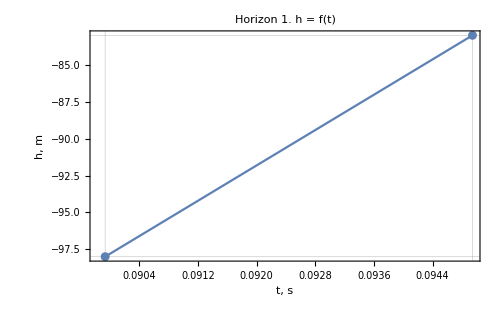
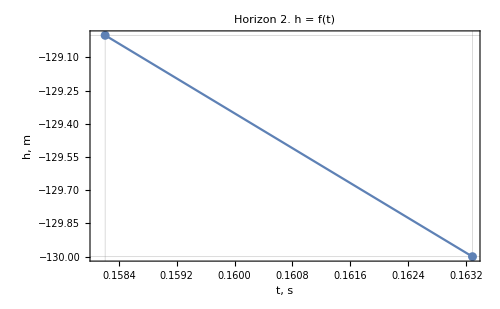
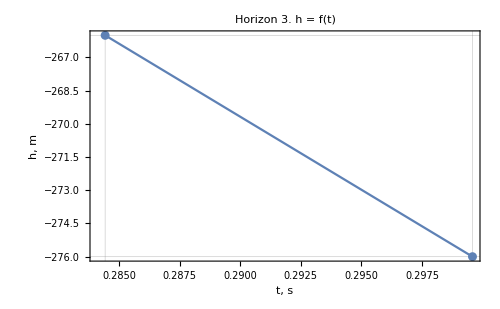

```mathematica
PlotHT[dataWellsHT,lmSetHT, t]
```

### VT

```mathematica
Clear[t]
lmSetVT=VT[datasetWells,datasetVelModel,timeNH, t][["lmSetVT"]]
setVT=VT[datasetWells,datasetVelModel,timeNH, t][["setVT"]]
atbt=VT[datasetWells,datasetVelModel,timeNH, t][["atbt"]]
fitParams=VT[datasetWells,datasetVelModel,timeNH, t][["fitParams"]]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{FittedModel[1000.],FittedModel[2000.+1.34348×10^-9 t],FittedModel[3000.+3.19534×10^-9 t],FittedModel[4000.+8.34503×10^-10 t]}

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{{{1,0.,1000},{1,0.,1000}},{{2,0.0899322,2000},{2,0.0949444,2000}},{{3,0.158208,3000},{3,0.163293,3000}},{{4,0.284427,4000},{4,0.299589,4000}}}

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{{{0,0.},{3,0.},{6,0.},{9,0.},{12,0.},{15,0.},{18,0.},{21,0.},{24,0.},{27,0.},{30,0.},{33,0.},{36,0.},{39,0.},{42,0.},{45,0.},{48,0.},{51,0.},{54,0.},{57,0.},{60,0.},{63,0.},{66,0.},{69,0.},{72,0.},{75,0.},{78,0.},{81,0.},{84,0.},{87,0.},{90,0.},{93,0.},{96,0.}},{{0,16.1756},{3,16.5086},{6,17.8545},{9,17.9018},{12,19.2108},{15,19.5782},{18,19.8187},{21,20.6266},{24,20.7452},{27,20.7485},{30,20.1898},{33,20.7435},{36,20.239},{39,19.6535},{42,19.4787},{45,18.8651},{48,19.0807},{51,18.6222},{54,18.6649},{57,18.2408},{60,17.9928},{63,17.9928},{66,18.0289},{69,18.7087},{72,18.8572},{75,19.0402},{78,19.768},{81,21.0029},{84,21.0958},{87,21.2979},{90,23.1322},{93,23.49},{96,24.3547}},{{0,75.0898},{3,70.7294},{6,70.0942},{9,66.8187},{12,66.2255},{15,63.7619},{18,61.5222},{21,61.8417},{24,61.463},{27,61.346},{30,60.5363},{33,62.9837},{36,64.1135},{39,65.5546},{42,67.958},{45,70.0573},{48,74.1028},{51,75.193},{54,77.1939},{57,79.317},{60,79.9825},{63,79.532},{66,79.9936},{69,80.2335},{72,77.3577},{75,75.5074},{78,73.968},{81,73.1759},{84,68.7619},{87,65.0798},{90,64.8555},{93,62.463},{96,60.4703}},{{0,323.595},{3,288.765},{6,263.563},{9,234.658},{12,219.656},{15,206.207},{18,194.56},{21,192.655},{24,195.298},{27,198.529},{30,200.363},{33,211.878},{36,222.845},{39,234.975},{42,248.71},{45,257.773},{48,273.671},{51,291.046},{54,305.11},{57,315.786},{60,329.984},{63,346.291},{66,359.014},{69,347.98},{72,336.685},{75,314.562},{78,293.557},{81,271.612},{84,241.955},{87,219.136},{90,204.008},{93,187.224},{96,175.245}}}

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{{1000.,0.},{2000.,1.34348×10^-9},{3000.,3.19534×10^-9},{4000.,8.34503×10^-10}}

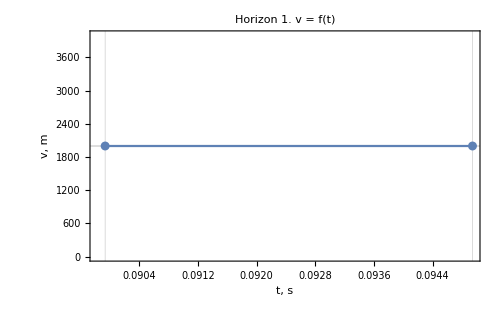
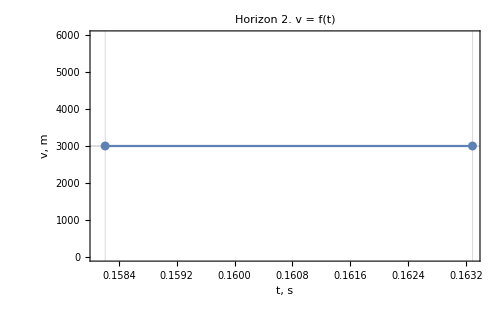
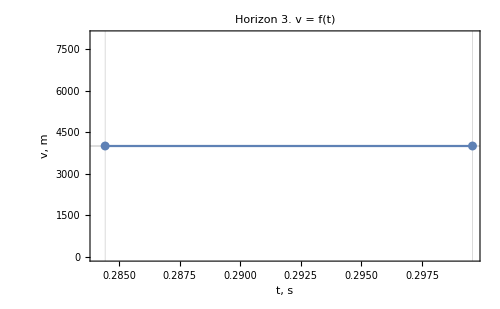

```mathematica
PlotVT[setVT,lmSetVT, t]
```